```mathematica
Nt = 551 ;(*151*)
ti = 0; tf =1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 2*Pi;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.159155

```mathematica
(*deltat = deltax * 0.2;*)

h = N[(2*Pi)/ (Nx),32];
(*deltax = h;*)

(*X2=Table[xi+(xf-xi) (i-1)/Nx,{i,1,Nx}]//N;*)

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

(*f[x_] =ⅇ^(- 4(x-π)^2);
f[x_]=f[xi+(((xf-xi)/(2 π))* x)];*)

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];
(*X = xi + (X)*((xf-xi)/(2*Pi))*)

(*deltax = (Last[X] - X[[1]]) / Nx*)
(*deltax = X[[2]] - X[[1]];*)

(*X = Table[(i-1)*h,{i,1,Nx }]//N;*)


f[x_] = ⅇ^(- 8(x-π)^2);
(*fo[x_] =ⅇ^(- 4(x-π)^2);*)
(*f[x_] = ⅇ^(- 4((((x-xi)*((2*Pi))/(xf-xi)))-π)^2)*)
(*f[x_] =ⅇ^(- 4(((x-xi)*((2*Pi))/(xf-xi))-π)^2);*)
(*T = Array[#&,Nt,{ti,tf}]//N;
X = Array[#&,Nx,{xi,xf}]//N;*)

(*X = Table[(i-1)*h,{i,1,Nx }]//N;
T = Table[(i-1)*deltat,{i,1,Nt }]//N;*)
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
D1[[4,1]]
```

```mathematica
-29.23288333488281
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((DL / 2)),32];
B = N[I1 + ((DL / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCN[[n+1,All]] = UCN[[n,All]] + (EMCN ).UCN[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*Euler*)
UEuler= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UEuler[[1,All]] = f[X];
UEuler = N[UEuler];
UEuler = Chop[N[UEuler], 10^(-307)];
UEuler = Developer`ToPackedArray[UEuler, Real]; 
Developer`PackedArrayQ[UEuler]

Ieuler = IdentityMatrix[Length[DL]];
MEuler = I1 +DL;

Do[UEuler[[n+1,All]] = MEuler.UEuler[[n,All]], {n,1,Nt - 1 }];
```

True

```mathematica
(*RK2*)
URK2= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK2[[1,All]] = f[X];
URK2 = N[URK2];
URK2 = Chop[N[URK2], 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]

IRK2 = IdentityMatrix[Length[DL]];
IRK2 = N[IRK2];

MRK2 = (IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2])));

EMRK2 = MRK2 - IRK2;

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*RK4*)
URK4= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK4[[1,All]] = f[X];
URK4 = N[URK4];
URK4 = Chop[N[URK4], 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]

IRK4 = IdentityMatrix[Length[DL]];
IRK4 = N[IRK4];

MRK4 = IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4]));

EMRK4 = MRK4 - IRK4;

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
(*LD4*)
UN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UN[[1,All]] = f[X];
UN = N[UN];
UN = Chop[N[UN], 10^(-307)];
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]


IN = IdentityMatrix[Length[D1]];
IN = N[IN];
AN = IN - ((DL / 2)) + (((MatrixPower[DL,2])/12));
AN = N[AN];
BN = IN + ((DL / 2)) + (((MatrixPower[DL,2])/12));
BN = N[BN];
MN = Inverse[AN].BN;
(*MN = N[MN,16];*)
EMN = MN - IN;

Do[UN[[n+1,All]] = UN[[n,All]] + (EMN).UN[[n,All]], {n,1,Nt - 1 }]
```

True

```mathematica
D1 = Developer`ToPackedArray[D1, Real];
```

```mathematica
(************************************************************************************************************************)

(* Eigenvalues*)
```

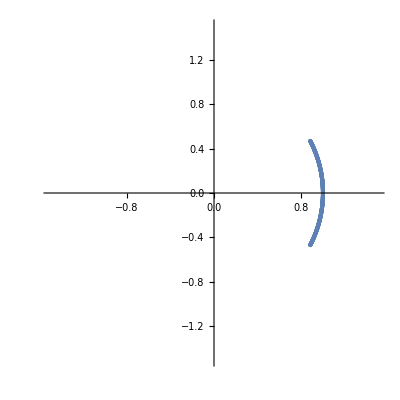

```mathematica
(*CN*)
evals = Eigenvalues[N[MCN]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

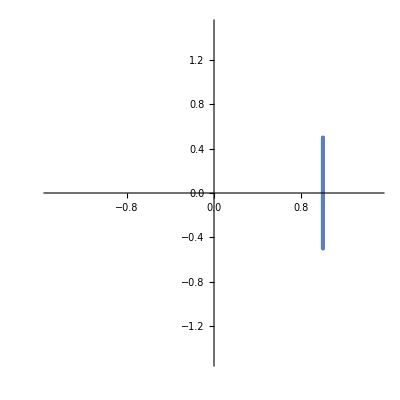

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[MEuler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
ListPlot[Transpose[{realEvalsEuler,imagEvalsEuler}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

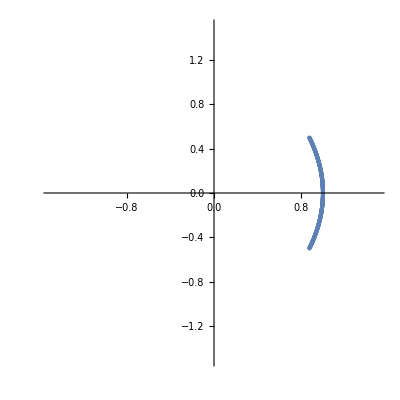

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

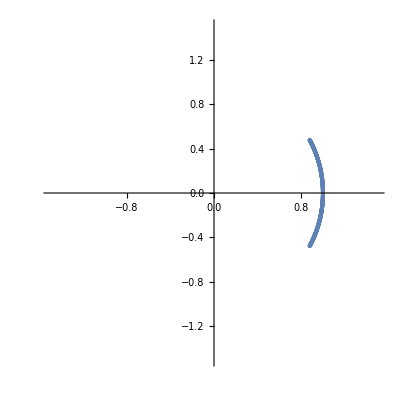

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

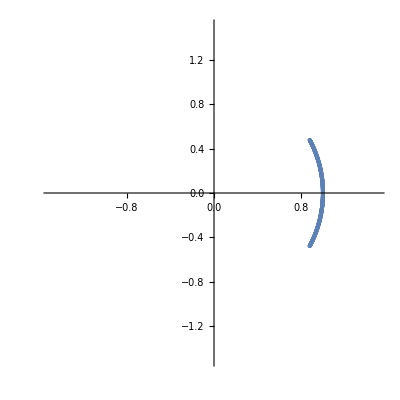

```mathematica
(*New Method*)
evalsN = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

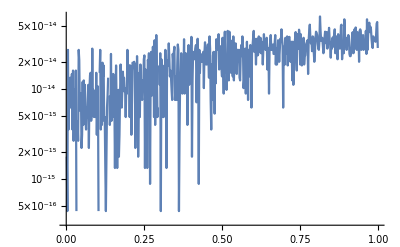

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];
energyErrorLD2 = Abs[intCN - intCN[[1]]];
ListLogPlot[{Transpose[{T,energyErrorLD2}]},PlotRange->{All,All},Joined->True]
```

```mathematica
(*Euler*)
FEuler = Table[0,{i,1,Nt},{j,1,Nx}];
intEuler = Table[0,{i,1,Length[FEuler[[All,1]]]}];
Do[
FEuler[[i]] = (D1.UEuler[[i,All]])^2;

intEuler[[i]] = (2π)/Nx Total[FEuler[[i,All]]]
,{i,1,Length[FEuler[[All,1]]]}];
(*ListPlot[{Transpose[{T,intEuler}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK2*)
FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
Do[
FRK2[[i]] = (D1.URK2[[i,All]])^2;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
Do[
FRK4[[i]] = (D1.URK4[[i,All]])^2;

intRK4[[i]] = (2π)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];
(*ListPlot[{Transpose[{T,intRK4}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*LD4*)
FN = Table[0,{i,1,Nt},{j,1,Nx}];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
Do[
FN[[i]] = (D1.UN[[i,All]])^2;

intN[[i]] = (2π)/Nx Total[FN[[i,All]]]
,{i,1,Length[FN[[All,1]]]}];
(*ListPlot[{Transpose[{T,intN}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*Exact*)
F = f[X];
F' = f'[X];
fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
(*fexact[t_,x_] = ⅇ^(- 4((x-t)-π)^2);
fexact[t_,x_] = ⅇ^(- 4((((x-xi)*((2*Pi))/(xf-xi))-t)-π)^2);*)
(*fexact[t_,x_] = ⅇ^(-4 (-π+1/50 π (50+(x - t)))^2);*)
(*fexact[t_,x_]=fexact[t,(x-xi)*((2*Pi))/(xf-xi)];*)
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
FEnergy = Table[0,{i,1,Nt},{j,1,Nx}];
intEnergy = Table[0,{i,1,Length[FEnergy[[All,1]]]}];
Do[
FEnergy[[i]] = (F')^2;

intEnergy[[i]] = (2*Pi)/Nx Total[FEnergy[[i,All]]];
,{i,1,Length[FEnergy[[All,1]]]}];
(*ListPlot[{Transpose[{T,intEnergy}]},Joined->True]*)
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD4 = Abs[intN - intN[[1]]];
energyErrorRK2 = Abs[intRK2 - intRK2[[1]]];
energyErrorRK4 = Abs[intRK4 - intRK4[[1]]];
```

```mathematica
(*LD2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD2}], PlotRange->Full]*)
```

```mathematica
(*LD4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD4}], PlotRange->Full]*)
```

```mathematica
(*RK2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK2}], PlotRange->Full]*)
```

```mathematica
(*RK4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK4}], PlotRange->Full]*)
```

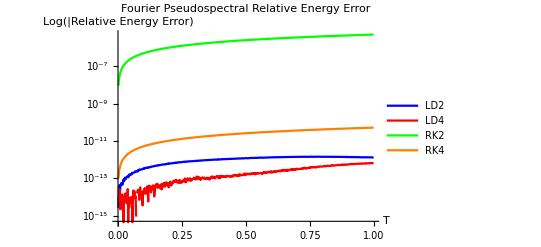

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotStyle->{Blue, Red,Green, Orange},PlotLegends->{"LD2","LD4","RK2","RK4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(*ListLinePlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotRange->{{ti,tf},{0,Max[energyErrorLD2]}}]*)
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(*L1 Error*)
```

```mathematica
(*Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = N[Uexact];
Uexact = Chop[N[Uexact], 10^(-307)];*)
(*Map back to original grid*)
(*Do[
Uexact[[i,All]] = xi + ((Uexact[[i,All]])*((xf-xi)/(2*Pi)))
,{i,1,Length[Uexact]}]*)
(*fexact[t_,x_] = ⅇ^(- 4((x-t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];*)
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
maxabserrLD2 = Table[0,{i,1,Length[abserrLD2]}];
Do[
abserrLD2[[i,All]] = UCN[[i,All]] - Uexact[[i,All]];
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
maxabserrLD2[[i]] = Max[abserrLD2[[i,All]]];
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
maxabserrRK2 = Max[abserrRK2]
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

0.0000483964

```mathematica
(*LD4*)
abserrLD4 = Abs[UN-Uexact];
maxabserrLD4 = Max[abserrLD4]
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

8.89931×10^-11

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
maxabserrRK4 = Max[abserrRK4]
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}],PlotRange->All]*)
```

5.33909×10^-10

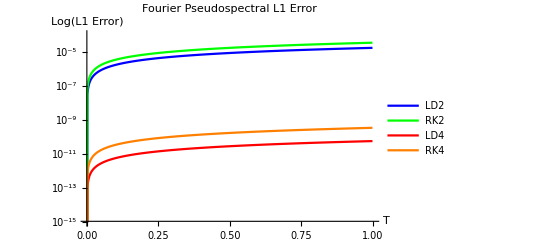

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue,Green,Red,Orange},PlotLegends->{"LD2","RK2","LD4","RK4"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,UCN[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{0,2*Pi},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,(UCN[[n]] - Uexact[[n]])}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```

```mathematica
(********************************************************************************************************************)
(*Start/Final*)

(*LD2*)
LD2start = UCN[[1]];
LD2startErr = UCN[[1]] - Uexact[[1]];
LD2end = Last[UCN];
LD2endErr = Last[UCN] - Last[Uexact];

(*LD4*)
LD4start = UN[[1]];
LD4startErr = UN[[1]] - Uexact[[1]];
LD4end = Last[UN];
LD4endErr = Last[UN] - Last[Uexact];

(*RK2*)
RK2start = URK2[[1]];
RK2startErr = URK2[[1]] - Uexact[[1]];
RK2end = Last[URK2];
RK2endErr = Last[URK2] - Last[Uexact];

(*RK4*)
RK4start = URK4[[1]];
RK4startErr = URK4[[1]] - Uexact[[1]];
RK4end = Last[URK4];
RK4endErr = Last[URK4] - Last[Uexact];

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final_PS.dat",exportData,"Table"];*)
```